```mathematica
c := 3*10^(10) 
G:= 6.67*10^(-8)
ρ0 :=  1.84*10^(-8) (* este es el valor que usamos en la tesis*)
ati := 2.5*10^(-9)
n := 2
```

```mathematica
k := (4π *G)/(3*c^2)*ρ0 *(ati)^(3-n)
```

```mathematica
k
```

1.42801×10^-44

```mathematica
ti := 0.74 (*s*)
Hti := 0.67 (* 1/s*)
Dati := Hti * ati (* 1/s*)
```

```mathematica
NDSolve[{a''[t]*a[t]+(a'[t])^2 -k*a[t]==0, a[ti]== ati, a'[ti] == Dati}, a, {t, ti, 10^4}]
```

{{a→InterpolatingFunction[…]}}

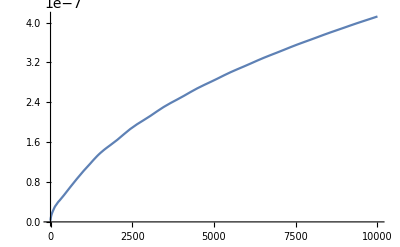

```mathematica
Plot[[x],{x,0.74,10000.}]
```

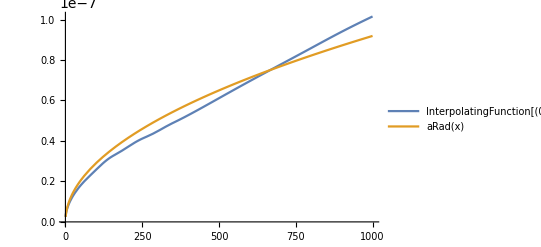

```mathematica
Plot[{[x],aRad[x]},{x,0.74,1000.}, PlotLegends->"Expressions"]
```